Kontinuierliches Model der Bewegung

```mathematica
𝒢=6.67428*10^(-11);
ℳ=6.0*10^24;
ℛ=6.357*10^6;
deq={
x''[t]==-𝒢 ℳ/(x[t]^2+y[t]^2)*x[t]/Sqrt[x[t]^2+y[t]^2],
y''[t]==-𝒢 ℳ/(x[t]^2+y[t]^2)*y[t]/Sqrt[x[t]^2+y[t]^2],
x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0};
```

Stabile Umlaufbahn bei ℛ+500000 km

```mathematica
r1=ℛ+100000;
v=Sqrt[𝒢*ℳ/r1]
te=2*2Pi r1/v
```

7875.22

10303.3

```mathematica
deq/.{x0:>0,y0:>-r1,vx0:>v,vy0:>0};
{solx,soly}={x,y}/.First@NDSolve[%,{x,y},{t,0,te}];
```

```mathematica
Manipulate[
Show[{
Graphics[{Blue,Opacity[0.5],Disk[{0,0},ℛ]}],
ParametricPlot[{solx[t],soly[t]},{t,0,tee},PlotStyle->{Red}]
},PlotRange->({{-#,#},{-#,#}}&@(1.1r1))],{tee,1,te}]
```

Simulator

Hier sind die Gleichungen (6), (7) und (8) implementiert. Die iterFunc nimmt x_tund berechnet daraus x_(t+1). ControlFunc kann benutzt werden um einen Agenten zu simulieren. Sie bekommt in jedem Schritt den aktuellen {x,y} Wert und muss ΔV in der Art {vx,vy} zurueck liefern.

```mathematica
dt=1.0;
Simulator[{x0_,v0_},te_Integer,controlFunc_]:=
Module[{iterFunc},
iterFunc[{st_,vt_}]:=With[{gt=-𝒢*ℳ/Norm[st]^2*st/Norm[st],
dv=controlFunc[st]},
Block[{stt=st+(vt*dt)+1/2*(gt+dv)*dt^2,gtt},
gtt=-𝒢*ℳ/Norm[stt]^2*stt/Norm[stt];
{stt,vt+(dv+(gt+gtt)/2)*dt
}]];
NestList[iterFunc,{x0,v0},te]
];
```

Gleiche Startwerte wie bei dem Differentialgl.-Sys. oben.

```mathematica
res=Simulator[{{0,-r1},{v,0}},IntegerPart[te],{0,0}&];
{simSolx,simSoly}=ListInterpolation[#,{{0,IntegerPart[te]}}]&/@Transpose[res[[All,1]]];
```

Der Unterschied zwischen Simulation und Loesen der Differentialgleichungen..

Hier der Gesamtunterschied der beiden Satellitenbahnen bei 2 Umlaeufen.

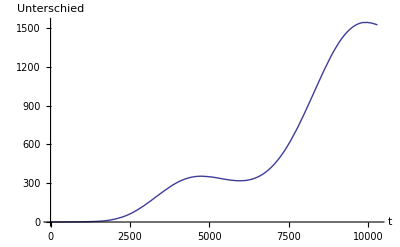

```mathematica
Plot[{(solx[t]-simSolx[t])^2+(soly[t]-simSoly[t])^2},{t,0,te},AxesLabel->{"t","Unterschied"}]
```

Hohmann-Bewegung.

Hier wollen wir versuchen von der stabilen Bahn r1 auf eine andere Bahn r2 zu gelangen. Dabei werden wir zuerst mal test, ob wir mit dem kont. Model nach der richtigen Zeit auch auf dem richtigen Radius r2 angekommen sind.

```mathematica
r1=100000+ℛ;
r2=5000000+ℛ;
v=Sqrt[𝒢*ℳ/r1];
mu=𝒢*ℳ;
dv1=Sqrt[mu/r1]*(Sqrt[2*r2/(r1+r2)]-1)
th=Pi*Sqrt[(r1+r2)^3/(8 mu)]
```

1017.38

4173.2

Das heisst, wenn wir zu unserer Anfangsgeschw. noch dv1 addieren, dann muessten wir nach th sekunden zum einen am Radius r2 angekommen sein und zum zweiten genau den Scheitelpunkt der ausgefuehrten Ellipse erreicht haben. Die Zahl im Plot gibt an, wie weit wir noch vom r2 entfernt sind.

```mathematica
deq/.{x0:>0,y0:>-r1,vx0:>v+dv1,vy0:>0};
{solx2,soly2}={x,y}/.First@NDSolve[%,{x,y},{t,0,th}];
Manipulate[
Show[{
Graphics[{Text[r2-Norm[{solx2[tee],soly2[tee]}],{-r1,-r2}],Blue,Opacity[0.5],Disk[{0,0},ℛ]}],
ParametricPlot[{solx2[t],soly2[t]},{t,0,tee},PlotStyle->{Red}]
},PlotRange->({{-#,#},{-#,#}}&@(1.2 r2))]
,{tee,1,th}]
```

Diskreter Fall

```mathematica
res=Simulator[{{0,-r1},{v+dv1,0}},IntegerPart[th],{0,0}&];
resCorrected=Simulator[{{0,-r1},{v+dv1-0.0012,0}},IntegerPart[th],{0,0}&];
```

Man sieht, dass das Quadrat der Abweichung ca 250 km am Endpunkt ist. Die von Hand korregierte Version kriegt etwas weniger Geschwindigkeit (0.0012 km/s).

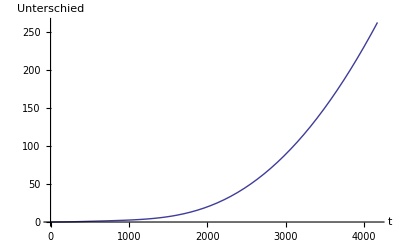

```mathematica
{simSolx,simSoly}=ListInterpolation[#,{{0,IntegerPart[th]}}]&/@Transpose[res[[All,1]]];
Plot[{(solx2[t]-simSolx[t])^2+(soly2[t]-simSoly[t])^2},{t,0,th},AxesLabel->{"t","Unterschied"}]
```

Korregierte Version (man achte auf die Skala).

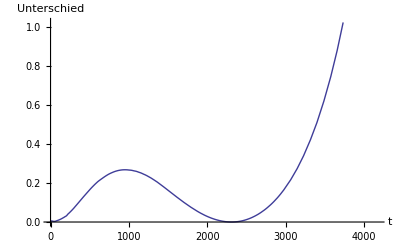

```mathematica
{simSolx,simSoly}=ListInterpolation[#,{{0,IntegerPart[th]}}]&/@Transpose[resCorrected[[All,1]]];
Plot[{(solx2[t]-simSolx[t])^2+(soly2[t]-simSoly[t])^2},{t,0,th},AxesLabel->{"t","Unterschied"}]
```